# Bosonic Complexity of Purification (BCoP)

IMPORTANT: Please read the instructions/advice carefully before running the file.

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import["/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/GaussianOptimization.m"]
```

```mathematica
(*<<GaussianOptimization`*)
```

In this Mathematica notebook we use the optimization procedure to find the complexity of purification for two bosonic systems. The first system, studied in the first Chapter is a lattice free scalar field theory with periodic conditions. This Chapter is called Bosons on a Periodic Lattice.
 
The second system, studied in the second Chapter, as a free scalar field theory undergoing a smooth quench through a critical point. This Chapter is called Bosons under a Smooth Quench Through a Critical Point.

## Chapter 1: Bosons on a Periodic Lattice

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for a bosonic system on a periodic lattice. The SubChapter: Definitions, should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

This part of the notebook is divided into  four scenarios. Each one of these is also divided into several sections, each one with a number of subsections. These are organized as follows:

1. In Scenario 1 we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N  with variable subsystem sizes dim1 and dim2 for different values of the mass of the scalar field m.

2. In Scenario 2 we look at BCoP, as a function of subsystem size dim1 dim2 with fixed d=0 lattice separation between subsystems for a scalar field mass of m=1/10 with variable N.

3. In Scenario 3 we look at BCoP, as a function of subsystem size dim1 dim2 with variable lattice separation d between subsystems for a scalar field mass of m=1/10 with variable N.

4. In Scenario 4 we look at BCoP, as a function of total number of lattice sites N with fixed subsystem size dim1 dim2 for a scalar field mass of m=1/10 with variable subsystem separation d.

In each Scenario, there are several Cases that are studied individually, where the rest of the parameters is varied. Each Case is divided into Subcases. At the end of each Case, a Summary for the Case contains the relevant outcome of the numerical optimization for the given Case. After all the cases have been studied for a given Scenario, a Summary for the Scenario is presented, with the relevant information for the setup.

Definitions (Run)

The following definitions are equivalent to the ones used in Michal and Lucas’ recent work on complexity for the thermofield double theory. The parameters of the theory are the following:

1. Total number of lattice sites: N,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: l,
4. Dimension of subsystems on the lattice: dim1 & dim2,
5. Lattice Site Separation between the subsystems: d,
6. Total length of the circle: L==(N-1)l .

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) CM[N,m,l], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) partialCM[N,m,l,d,dim1,dim2].

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

Scenario 1: BCoP as a Function of Subsystem Partition Separation (Fixed Bipartite Subsystem Size) with m=1/10:

In this Scenario, we look at bosonic complexity of purification BCoP, as a function of lattice separation d between subsystems with fixed total number of sites N for a scalar field mass of m=1/10 with variable subsystem sizes dim1 and dim2. This scenario is interesting, as it will tell us about the behaviour of complexity of purification in the case where the subsystem in a mixed state is comprised of two regions in the lattice. By varying the separation between the regions that make up the subsystem, we can study the effect that separating the subregions has on the complexity of the purified state.

This Scenario consists of 5 Cases. The difference between the Cases studied is the total length L of the periodic lattice.

1. Case 1: N=100, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1 ;  ( N-1)δ == L=99

2. Case 2: N=100, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1/10;  (N-1)δ == L=9.9

3. Case 3: N=10, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1 ;  (N-1)δ == L=9

4. Case 4: N=10, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1/10 ; (N-1)δ == L=0.9

5. Case 5: N=300,m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1 ; (N-1)δ == L=299

Each Case is followed by Subcases, where the dimension of the subsystem regions dim1 = dim2 is varied. For Each Subcase,  BCoP is calculated for a given subsystem region separation d. At the end of the Section, a graph is shown which presents the results of the optimization for BCoP as a function of subsystem separation: BCoP[d].

IMPORTANT: At the moment of writing this sentence (04.09.19 - 13:21), only Case 1 is being studied. Cases 2,3,4,5 are pending.

#### List of Updates

UPDATE (04.09.19 - 13:21): SubCases 1.1. , 1.2 , and 1.3 where studied a previous version of the Optimization Algorithm, which does not take into account the newest specifications (according to the .m file from 30.08.19). SubCase 1.4 is being studied with the most recent function definitions (version 04.09.19 by Lucas).

UPDATE (04.09.19 - 13:21): Results for SubCases 1.1, 1.2, and 1.3 can be found in a subsection within each section called Summary.

UPDATE (06.09.19 - 16:30): Simplified the analysis of results using the revised version of the Optimization package (version 06.09.19 by Lucas).

UPDATE (09.09.19 - 11:50): Optimized SubCase Analysis. SubCases 1.1. , 1.2 , and 1.3 are studied again with the newest Optimization Package.

UPDATE (10.09.19 - 11:30): Added an extra subcase to test symmetry in BCoP (Spolier alert: doesn’t seem to be symmetric under the exchange of partitions).

UPDATE (11.09.19 - 10:00): Added an extra subcase to test symmetry in BCoP going all the way with partition separation (Spolier alert: doesn’t seem to be symmetric under the exchange of partitions).

UPDATE (16.09.19 - 15:30): Implemented newest package changes by Lucas in SubCase 1.3 (and more initial matrices M0).

## Case 1: N=100, m=1/10, δ=1 ; (N-1)δ == L=99

### SubCase 1.1: N=100, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1, dimA1=dimB1=1

#### I. m=1/10

#### a). SubCase Parameters

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=1;
dimB1=1;
dimPur=dimA1+dimB1; (*Minimal Purification*)
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{9},{10},{11},{12},{15},{20},{30},{40},{50},{60},{70},{80},{85},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96},{97},{98}}; (*List of separation values*)
seplist=Flatten[Arrayseplist];
```

#### b). Initial Covariance Matrix

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist⟦i⟧,dimA1,dimB1],{i,1,Length[seplist]}];
```

#### c). Purified State Complex Structure

```mathematica
(*Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}];*)
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[seplist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
(*Here we can change the lower-right block structure of M0, if we wanted. Other possibilities are Inverse[MTra]*)
```

```mathematica
Length[M0]
Dimensions[M0]
```

32

{32,8,8}

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis]].LieBasis].M0⟦j⟧,{i,50}],{j,Length[seplist]}];
```

```mathematica
(*Here we generate 10 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List[[1]]]
```

32

{32,50,8,8}

{50,8,8}

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
geometry=GOGeometryConst[LieBasis,JR0,+1];
```

```mathematica
SystemSpecific=Table[{JR0,M0List⟦i⟧,LieBasis,geometry,newM},{i,Length[M0List]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific[[1]]]
```

32

{32,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Time=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,1⟧;
Result=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
Dimensions[Time]
```

{32}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{32,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {2.04732,1.85359,2.00903,1.93636,1.90792,1.82815,1.92662,1.89981,1.93557,1.94593,2.11001,2.04514,2.09275,2.0934,2.05107,2.07737,1.93681,2.02733,2.00825,1.91143,1.86761,2.05797,2.3801,2.51532,2.23781,2.11886,2.0169,2.01893,1.94618,1.89357,1.84845,1.9218} seconds

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {0.707459,0.767223,0.780635,0.787262,0.79114,0.793601,0.797171,0.797745,0.798164,0.798473,0.798703,0.799105,0.799346,0.799434,0.799442,0.799443,0.799441,0.799428,0.799284,0.798875,0.798473,0.798164,0.797745,0.797171,0.796373,0.795242,0.793601,0.79114,0.787262,0.780635,0.767223,0.707459}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,6,7,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,6,6,7,7,7,7,6,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

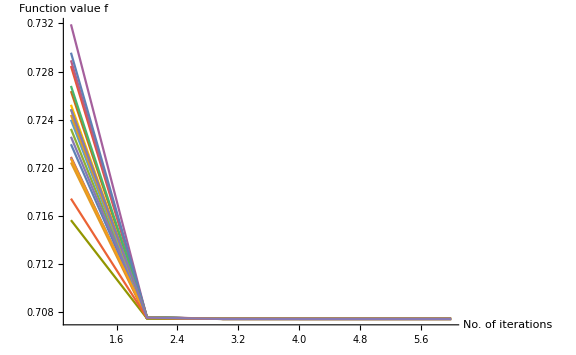
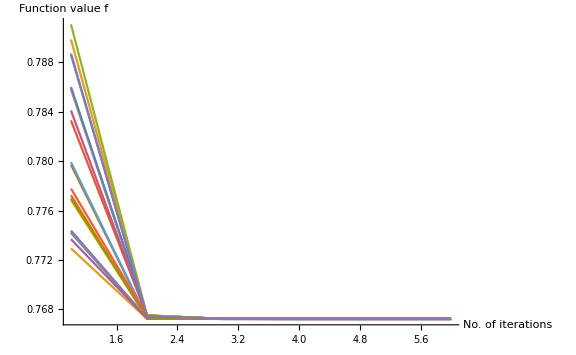
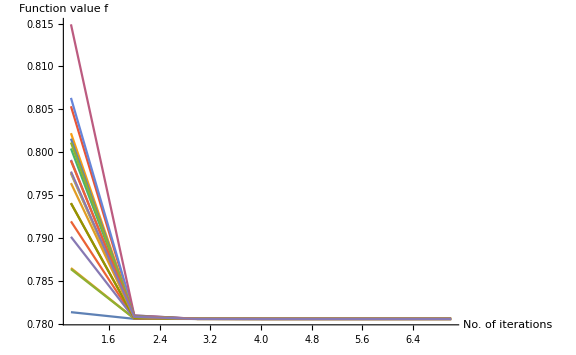
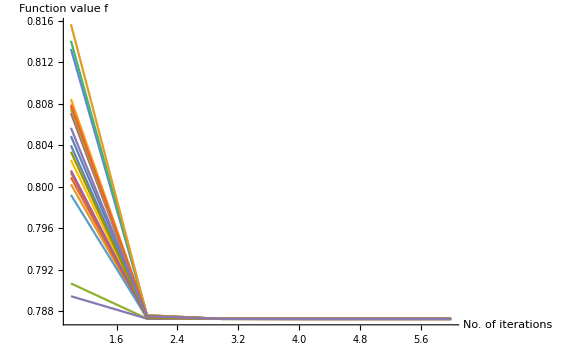
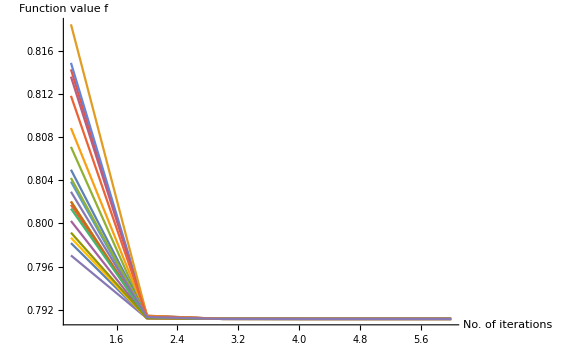
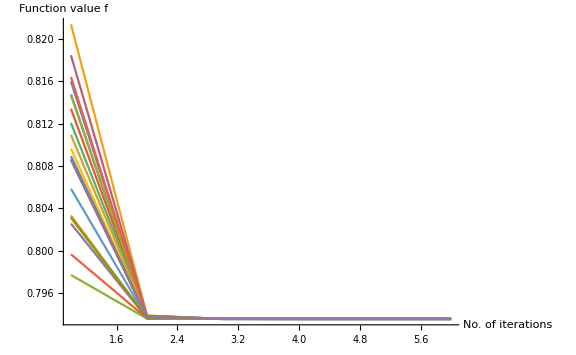
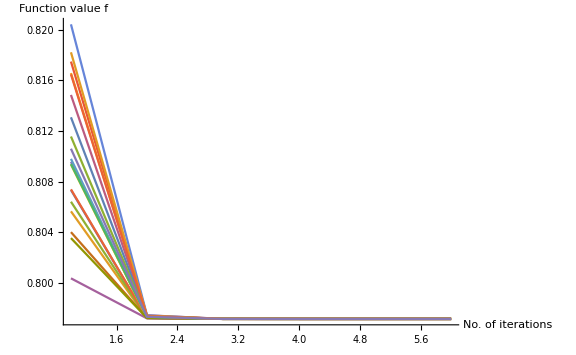
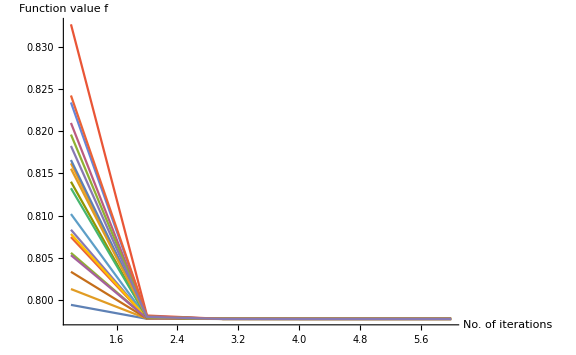

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

```mathematica
(*Expand the previous entry to view the convergence for the individual points in the optimization.*)
```

```mathematica
ListSubCase11new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
```

{{0,0.707459},{1,0.767223},{2,0.780635},{3,0.787262},{4,0.79114},{5,0.793601},{8,0.797171},{9,0.797745},{10,0.798164},{11,0.798473},{12,0.798703},{15,0.799105},{20,0.799346},{30,0.799434},{40,0.799442},{50,0.799443},{60,0.799441},{70,0.799428},{80,0.799284},{85,0.798875},{87,0.798473},{88,0.798164},{89,0.797745},{90,0.797171},{91,0.796373},{92,0.795242},{93,0.793601},{94,0.79114},{95,0.787262},{96,0.780635},{97,0.767223},{98,0.707459}}

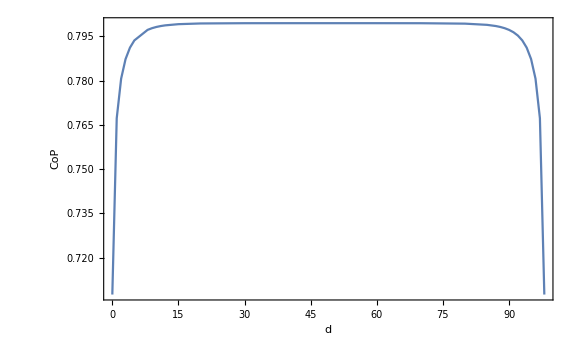

```mathematica
ListPlot[ListSubCase11new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

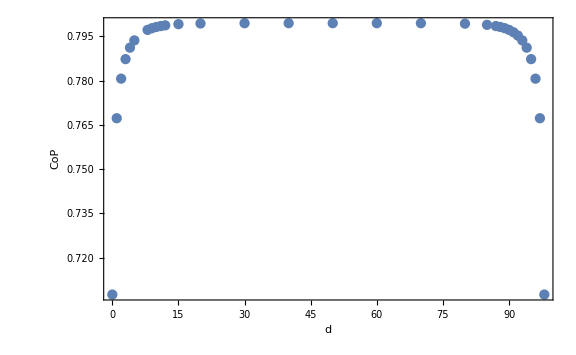
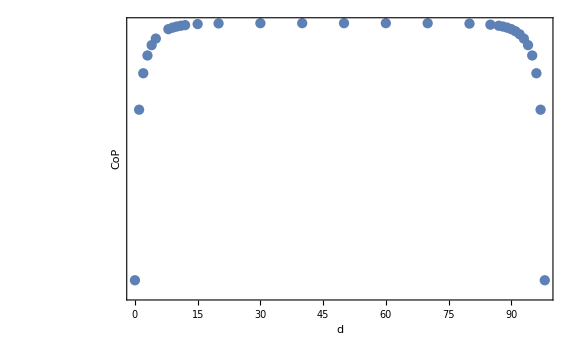

```mathematica
PlotListSubCase11new=Row[{ListPlot[ListSubCase11new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase11new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase11new.pdf",PlotListSubCase11new];
```

#### II. m=1/20

### SubCase 1.2: N=100, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1, dimA1=dimB1=2

#### a). SubCase Parameters

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=2;
dimB1=2;
dimPur=dimA1+dimB1; (*Minimal Purification*)
Arrayseplist={{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{15},{20},{30},{40},{50},{60},{70},{80},{85},{87},{88},{89},{90},{91},{92},{93},{94},{95},{96}}; (*List of separation values*)
seplist=Flatten[Arrayseplist];
```

#### b). Initial Covariance Matrix

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist⟦i⟧,dimA1,dimB1],{i,1,Length[seplist]}];
```

#### c). Purified State Complex Structure

```mathematica
(*Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}];*)
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[seplist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
(*Here we can change the lower-right block structure of M0, if we wanted. Other possibilities are Inverse[MTra]*)
```

```mathematica
Length[M0]
Dimensions[M0]
```

32

{32,16,16}

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis]].LieBasis].M0⟦j⟧,{i,20}],{j,Length[seplist]}];
```

```mathematica
(*Here we generate 20 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List[[1]]]
```

32

{32,20,16,16}

{20,16,16}

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
geometry=GOGeometryConst[LieBasis,JR0,+1];
```

```mathematica
SystemSpecific=Table[{JR0,M0List⟦i⟧,LieBasis,geometry,newM},{i,Length[M0List]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific[[1]]]
```

32

{32,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Time=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,1⟧;
Result=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
Dimensions[Time]
```

{32}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{32,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {4.07525,4.08865,3.84169,4.08247,4.12597,3.71445,4.47261,4.85002,4.02836,4.07634,4.08905,3.72292,3.82085,3.77029,4.08773,3.52014,3.80365,3.75453,3.962,3.9702,3.95344,3.8258,3.71019,4.00769,3.74583,4.03265,4.05346,3.90891,3.82529,4.11084,4.1454,3.85645} seconds

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {0.890738,0.956594,0.973802,0.982673,0.987995,0.991432,0.993754,0.995372,0.996523,0.997358,0.99797,0.998424,0.998764,0.999362,0.999723,0.999857,0.999869,0.99987,0.999867,0.999835,0.999476,0.998426,0.997362,0.99653,0.995382,0.993771,0.991461,0.988046,0.982771,0.974005,0.957094,0.892738}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,7,7,7,7,6,7,7,6,7,6,6,6,6,6,6,7,6,7,7,7,6,6,7,6,7,7,6,6,7,7,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

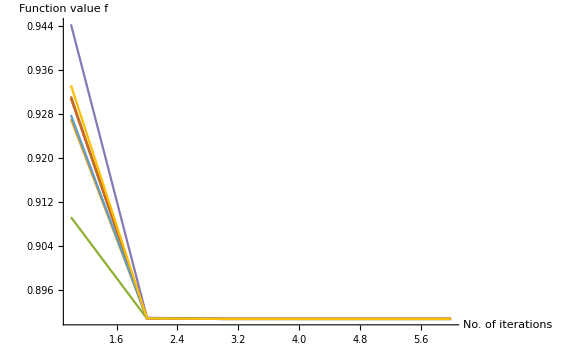
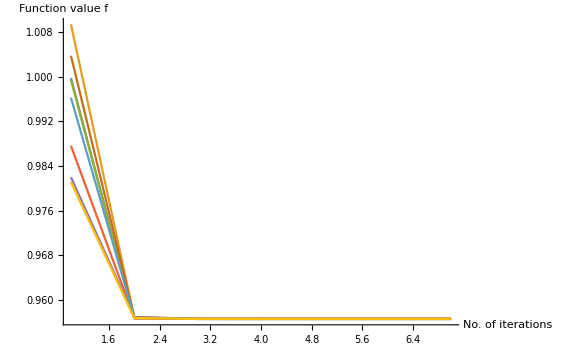
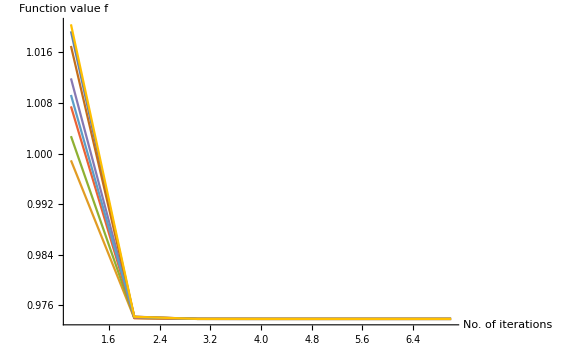
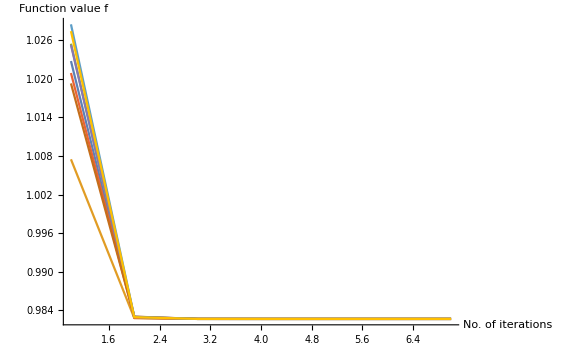
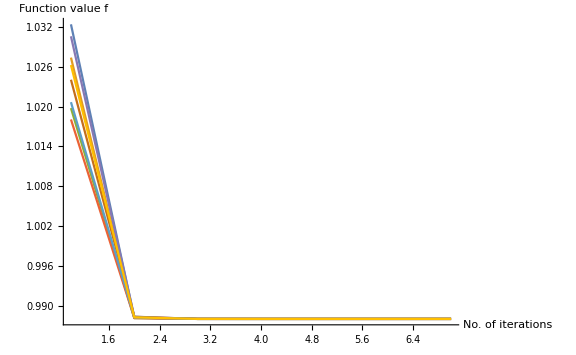
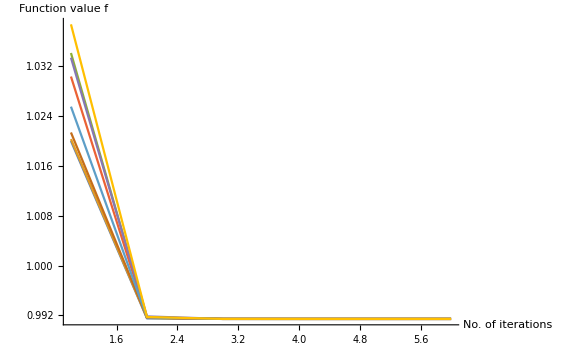
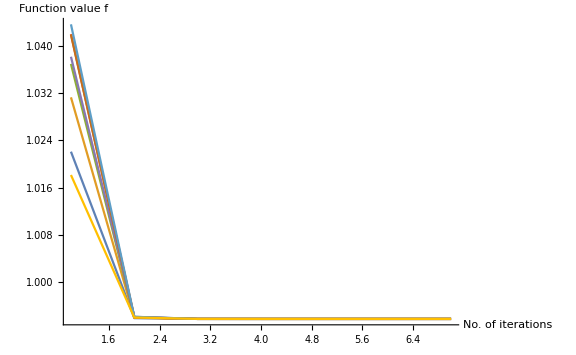
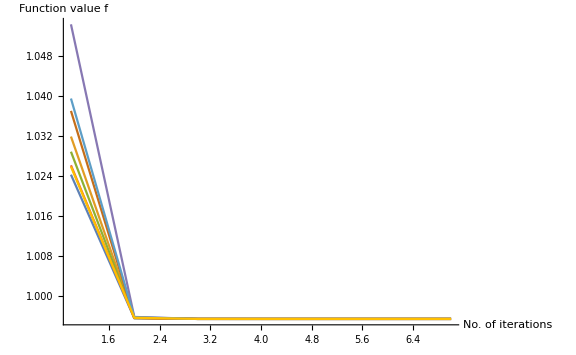

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

```mathematica
(*Expand the previous entry to view the convergence for the individual points in the optimization.*)
```

```mathematica
ListSubCase12new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
```

{{0,0.890738},{1,0.956594},{2,0.973802},{3,0.982673},{4,0.987995},{5,0.991432},{6,0.993754},{7,0.995372},{8,0.996523},{9,0.997358},{10,0.99797},{11,0.998424},{12,0.998764},{15,0.999362},{20,0.999723},{30,0.999857},{40,0.999869},{50,0.99987},{60,0.999867},{70,0.999835},{80,0.999476},{85,0.998426},{87,0.997362},{88,0.99653},{89,0.995382},{90,0.993771},{91,0.991461},{92,0.988046},{93,0.982771},{94,0.974005},{95,0.957094},{96,0.892738}}

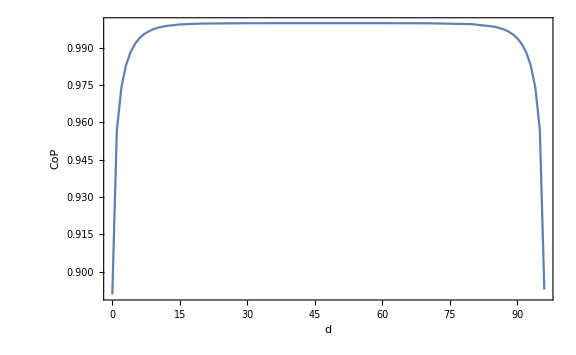

```mathematica
ListPlot[ListSubCase12new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

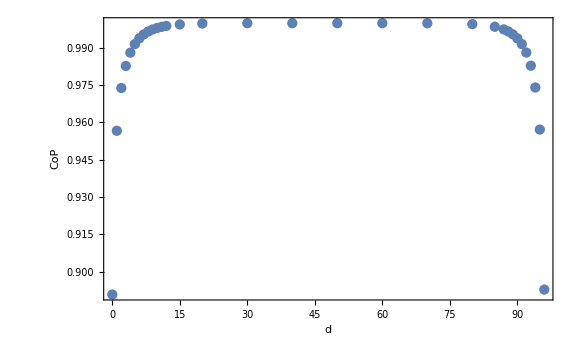
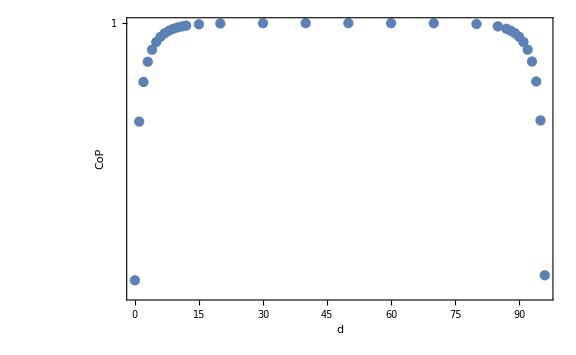

```mathematica
PlotListSubCase12new=Row[{ListPlot[ListSubCase12new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase12new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase12new.pdf",PlotListSubCase12new];
```

### SubCase 1.3: N=100, m={1/10,1/20,1/50,1/100,1/500,1/1000,1/2000}, δ=1, dimA1=dimB1=3

#### a). SubCase Parameters

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=3;
dimB1=3;
dimPur=dimA1+dimB1; (*Minimal Purification*)
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{50},{60},{70},{80},{85},{87},{88},{89},{90},{91},{92},{93},{94}}; (*List of separation values*)
seplist=Flatten[Arrayseplist];
```

#### b). Initial Covariance Matrix

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist⟦i⟧,dimA1,dimB1],{i,1,Length[seplist]}];
```

#### c). Purified State Complex Structure

```mathematica
(*Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}];*)
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[seplist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
(*Here we can change the lower-right block structure of M0, if we wanted. Other possibilities are Inverse[MTra]*)
```

```mathematica
Length[M0]
Dimensions[M0]
```

26

{26,24,24}

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis]].LieBasis].M0⟦j⟧,{i,10}],{j,Length[seplist]}];
```

```mathematica
(*Here we generate 10 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List[[1]]]
```

26

{26,10,24,24}

{10,24,24}

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
geometry=GOGeometryConst[LieBasis,JR0,+1];
```

```mathematica
SystemSpecific=Table[{JR0,M0List⟦i⟧,LieBasis,geometry,newM},{i,Length[M0List]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific[[1]]]
```

26

{26,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Time=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,1⟧;
Result=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
Dimensions[Time]
```

{26}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{26,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {5.8229,6.59806,7.87684,6.54063,6.72894,6.51921,6.37394,6.60105,6.4049,6.24866,6.60764,6.62658,6.41511,6.20189,6.10534,6.06321,6.07765,6.50662,6.39671,6.68429,6.44641,6.70696,6.11256,6.74441,6.328,6.03061} seconds

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {1.0354,1.09587,1.11317,1.12242,1.12812,1.13188,1.13761,1.13931,1.14026,1.14101,1.1415,1.14171,1.14174,1.14175,1.14173,1.14163,1.14082,1.13859,1.13631,1.13449,1.13192,1.12819,1.12254,1.11339,1.09643,1.03813}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,7,7,7,7,7,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,6,7,6,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

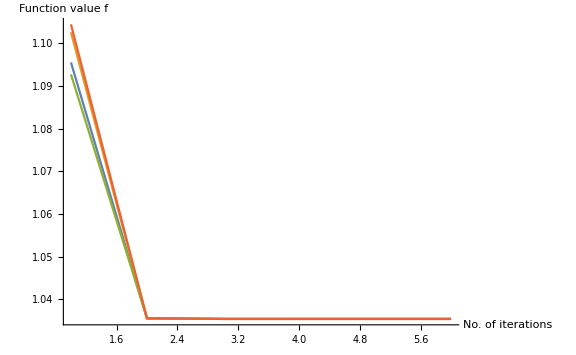
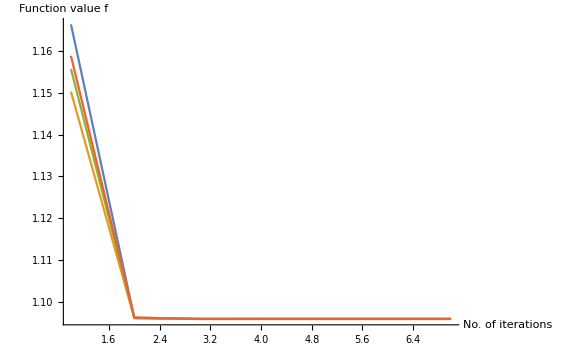
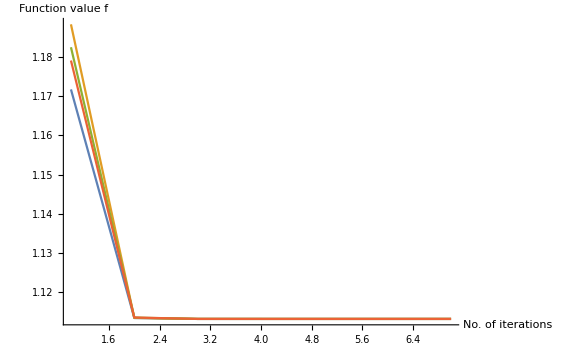
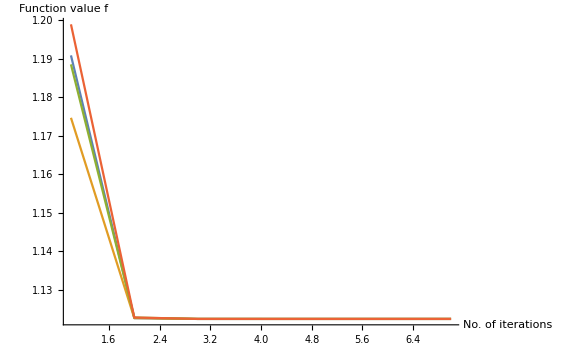
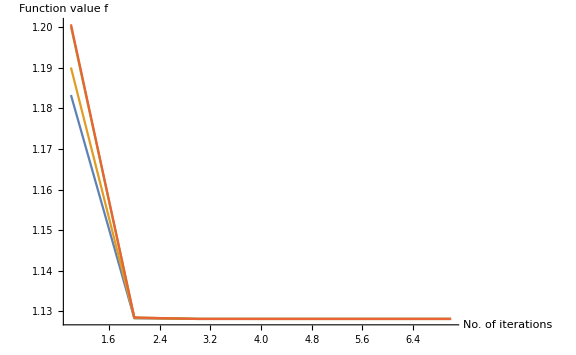
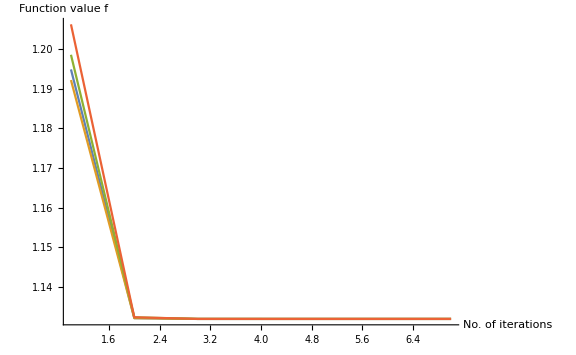
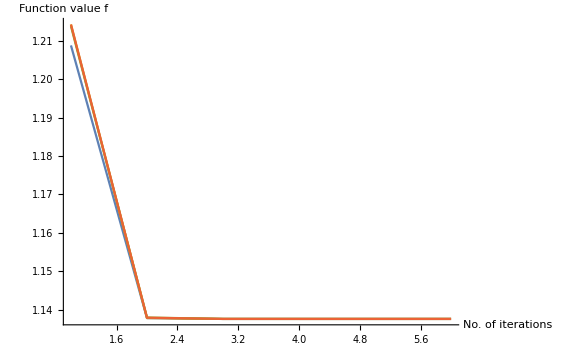
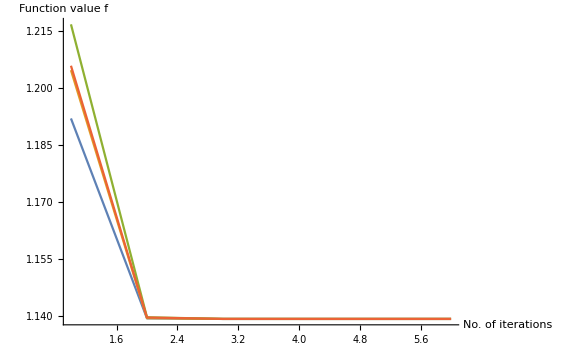

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

```mathematica
(*Expand previous entry to see convergence of individual points.*)
```

```mathematica
ListSubCase13new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
```

{{0,1.0354},{1,1.09587},{2,1.11317},{3,1.12242},{4,1.12812},{5,1.13188},{8,1.13761},{10,1.13931},{12,1.14026},{15,1.14101},{20,1.1415},{30,1.14171},{40,1.14174},{50,1.14175},{60,1.14173},{70,1.14163},{80,1.14082},{85,1.13859},{87,1.13631},{88,1.13449},{89,1.13192},{90,1.12819},{91,1.12254},{92,1.11339},{93,1.09643},{94,1.03813}}

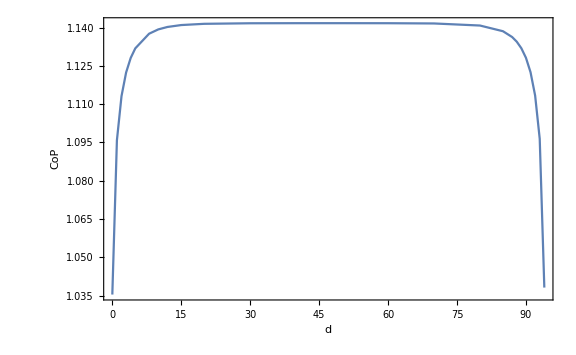

```mathematica
ListPlot[ListSubCase13new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

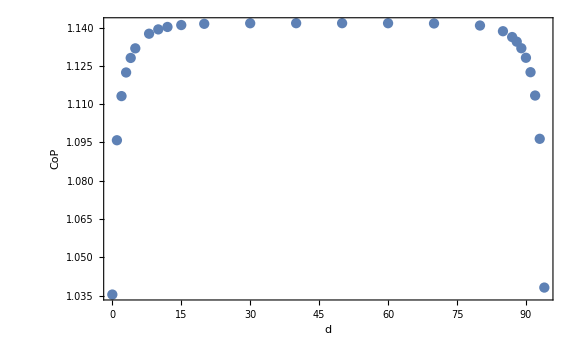
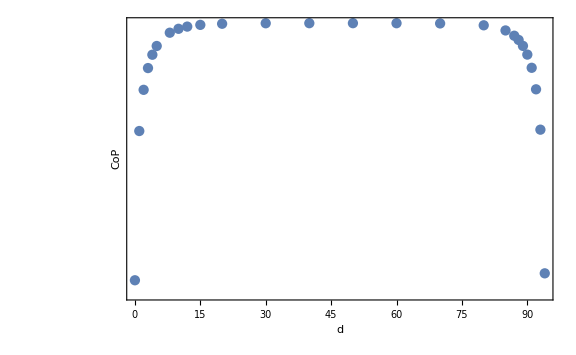

```mathematica
PlotListSubCase13new=Row[{ListPlot[ListSubCase13new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase13new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase13new.pdf",PlotListSubCase13new];
```

### Extra SubCase 3: N=100, m=1/10, δ=1, Different partition dimensions (Small subsystem size) Going all the way with separation

#### a) dimA1=1, dimB1=3

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=1;
dimB1=3;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{50},{60},{70},{80},{85},{88},{90},{91},{92},{93},{94},{95},{96}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.890909}

Reason for termination: Function value tolerance reached

{0.213958,{{0.890738},{SparseArray[…]},{3,3,3,3},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.28892,0.0193999,0.00131881,0.0000915685,6.62964×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.890738},{0.946472},{0.961211},{0.968975},{0.973707},{0.976809},{0.981528},{0.982928},{0.983728},{0.984365},{0.984789},{0.984974},{0.984994},{0.984995},{0.98499},{0.984941},{0.984492},{0.983379},{0.981522},{0.978925},{0.976794},{0.973687},{0.968945},{0.961164},{0.946372},{0.890143}}

```mathematica
ListSubCaseExtra3a=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

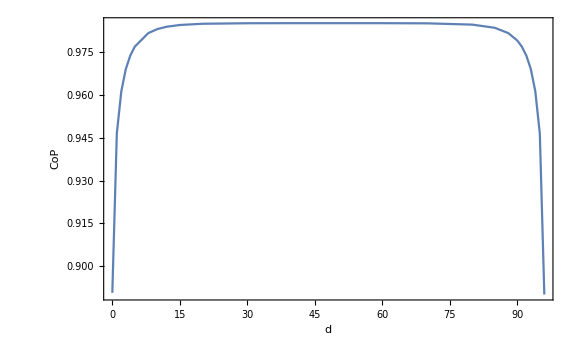

```mathematica
ListPlot[ListSubCaseExtra3a,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

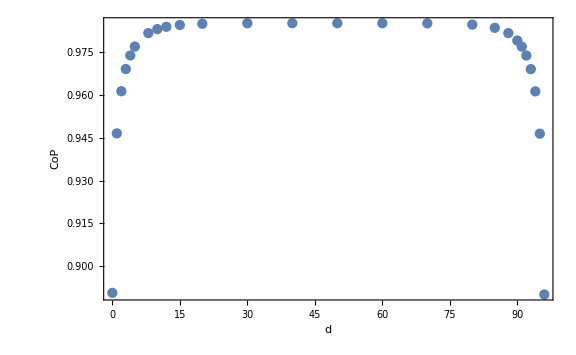
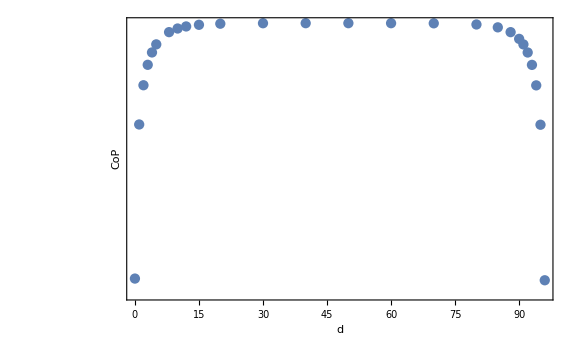

```mathematica
PlotListSubCaseExtra3a=Row[{ListPlot[ListSubCaseExtra3a,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCaseExtra3a,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCaseExtra3a.pdf",PlotListSubCaseExtra3a];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.219927,0.2407,0.250895,0.256839,0.257696,0.252877,0.256564,0.244239,0.235911,0.229645,0.238231,0.246226,0.219436,0.243242,0.238415,0.239225,0.222905,0.240675,0.25397,0.246605,0.229313,0.243544,0.237823,0.246279,0.227456,0.235119}

#### b) dimA1=3, dimB1=1

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=3;
dimB1=1;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{8},{10},{12},{15},{20},{30},{40},{50},{60},{70},{80},{85},{88},{90},{91},{92},{93},{94},{95},{96}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}];
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];
MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{0.890909}

Reason for termination: Function value tolerance reached

{0.20685,{{0.890738},{SparseArray[…]},{3,3,3,3},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.890909,0.890738,0.890738,0.890738,0.890738}},{{0.28892,0.0193999,0.00131881,0.0000915685,6.62964×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{0.890738},{0.950635},{0.965851},{0.973723},{0.978483},{0.981584},{0.986252},{0.987614},{0.988381},{0.988981},{0.989368},{0.989529},{0.989545},{0.989547},{0.989543},{0.989501},{0.9891},{0.988056},{0.986265},{0.983727},{0.981629},{0.978556},{0.973848},{0.9661},{0.951278},{0.893544}}

```mathematica
ListSubCaseExtra3b=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

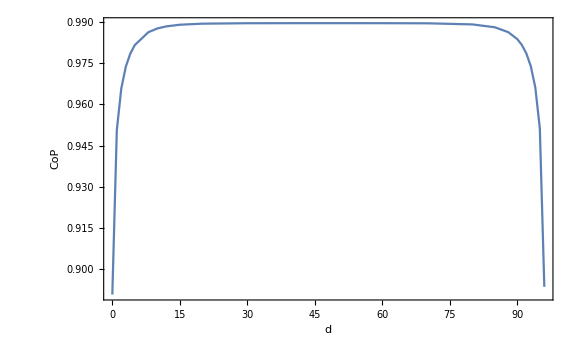

```mathematica
ListPlot[ListSubCaseExtra3b,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

Also in this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

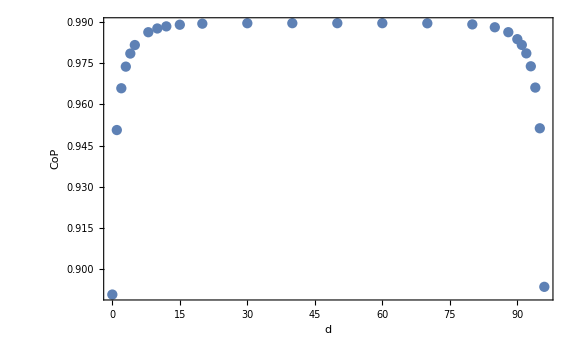
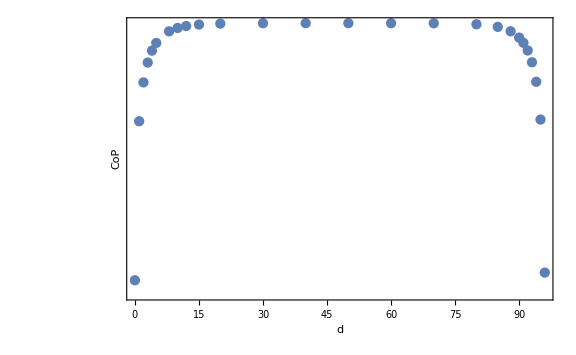

```mathematica
PlotListSubCaseExtra3b=Row[{ListPlot[ListSubCaseExtra3b,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCaseExtra3b,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCaseExtra3b.pdf",PlotListSubCaseExtra3b];
```

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{0.401627,0.62916,0.639944,0.606891,0.553317,0.654698,0.601997,0.589691,0.546838,0.627778,0.610417,0.613179,0.59877,0.508403,0.530557,0.549059}

#### c) Comparison

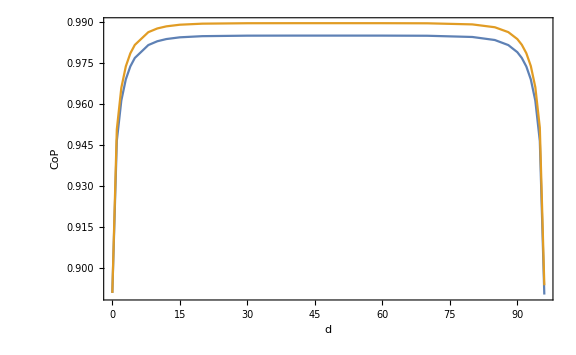

```mathematica
ListPlot[{ListSubCaseExtra3a,ListSubCaseExtra3b},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

### SubCase 1.4: N=100, m=1/10, δ=1, dimA1=dimB1=8

#### a). SubCase Parameters

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=8;
dimB1=8;
dimPur=dimA1+dimB1; (*Minimal Purification*)
Arrayseplist={{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{15},{20},{30},{40},{50},{60},{70},{72},{74},{75},{76},{77},{78},{79},{80},{81},{82},{83},{84}}; (*List of separation values*)
seplist=Flatten[Arrayseplist];
```

#### b). Initial Covariance Matrix

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist⟦i⟧,dimA1,dimB1],{i,1,Length[seplist]}];
```

#### c). Purified State Complex Structure

```mathematica
(*Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}];*)
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[seplist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
(*Here we can change the lower-right block structure of M0, if we wanted. Other possibilities are Inverse[MTra]*)
```

```mathematica
Length[M0]
Dimensions[M0]
```

32

{32,64,64}

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis]].LieBasis].M0⟦j⟧,{i,10}],{j,Length[seplist]}];
```

```mathematica
(*Here we generate 10 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List[[1]]]
```

32

{32,10,64,64}

{10,64,64}

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
geometry=GOGeometryConst[LieBasis,JR0,+1];
```

```mathematica
SystemSpecific=Table[{JR0,M0List⟦i⟧,LieBasis,geometry,newM},{i,Length[M0List]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific[[1]]]
```

32

{32,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Time=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,1⟧;
Result=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
Dimensions[Time]
```

{32}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{32,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {562.688,808.574,694.039,246.343,245.156,254.218,249.376,249.346,249.963,250.296,250.622,251.596,250.667,247.682,250.198,250.401,251.342,249.549,249.299,246.664,245.195,243.779,245.552,244.653,244.345,243.281,242.233,573.307,567.744,569.135,557.4,554.048} seconds

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {1.56955,1.60737,1.62036,1.62771,1.6324,1.63556,1.63778,1.63937,1.64053,1.64139,1.64204,1.64253,1.6429,1.64358,1.64402,1.64421,1.64424,1.64423,1.64415,1.64341,1.6429,1.64204,1.64139,1.64053,1.63937,1.63778,1.63557,1.63242,1.62776,1.62049,1.60778,1.57165}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

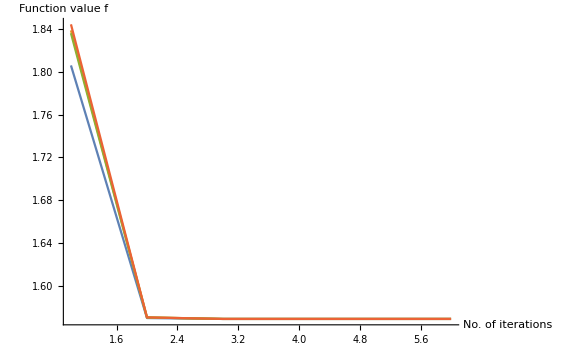
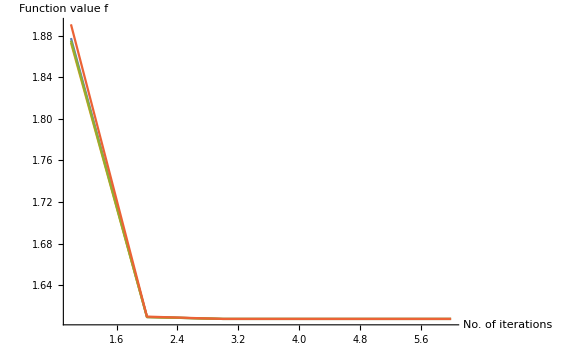
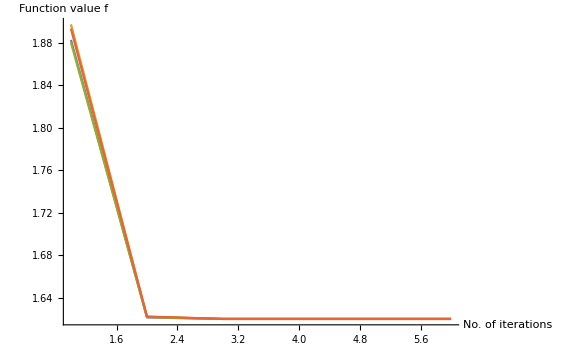
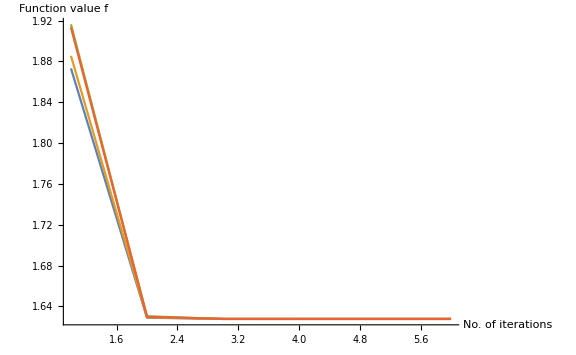
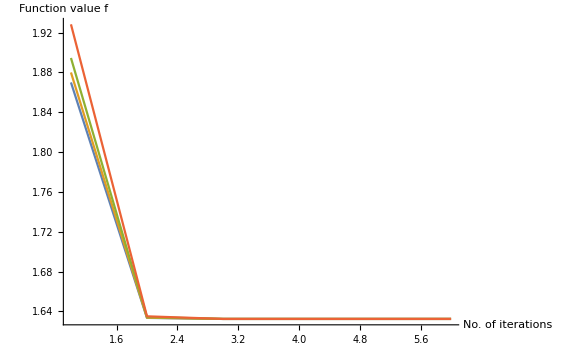
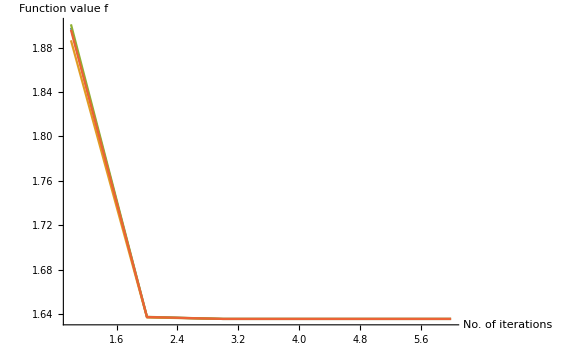
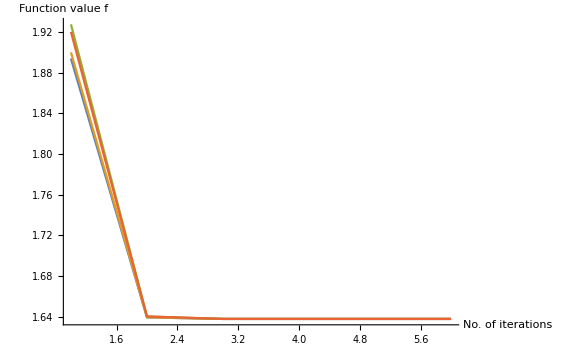
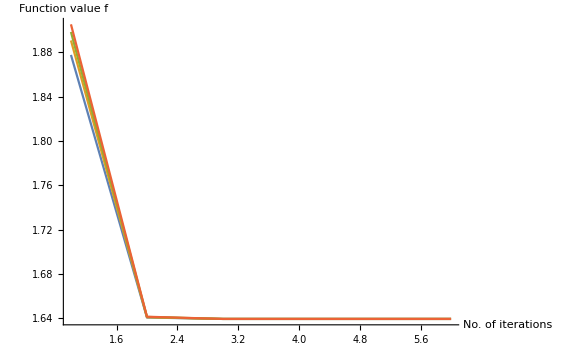
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

```mathematica
(*Expand the previous entry to view the convergence for the individual points in the optimization.*)
```

```mathematica
ListSubCase14new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
Export[NotebookDirectory[]<>"ListBCoPdimA18B18.txt",ListSubCase14new];
```

{{0,1.56955},{1,1.60737},{2,1.62036},{3,1.62771},{4,1.6324},{5,1.63556},{6,1.63778},{7,1.63937},{8,1.64053},{9,1.64139},{10,1.64204},{11,1.64253},{12,1.6429},{15,1.64358},{20,1.64402},{30,1.64421},{40,1.64424},{50,1.64423},{60,1.64415},{70,1.64341},{72,1.6429},{74,1.64204},{75,1.64139},{76,1.64053},{77,1.63937},{78,1.63778},{79,1.63557},{80,1.63242},{81,1.62776},{82,1.62049},{83,1.60778},{84,1.57165}}

```mathematica
ListPlot[ListSubCase14new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
PlotListSubCase14new=Row[{ListPlot[ListSubCase14new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListPlot[ListSubCase14new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase14new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase14new.pdf",PlotListSubCase14new];
```

-Graphics--Graphics--Graphics-

### SubCase 1.5: N=100, m=1/10, δ=1, dimA1=dimB1=10

#### a). SubCase Parameters

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=10;
dimB1=10;
dimPur=dimA1+dimB1; (*Minimal Purification*)
Arrayseplist={{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{15},{20},{30},{40},{50},{60},{65},{69},{70},{71},{72},{73},{74},{75},{76},{77},{78},{79},{80}}; (*List of separation values*)
seplist=Flatten[Arrayseplist];
```

#### b). Initial Covariance Matrix

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist⟦i⟧,dimA1,dimB1],{i,1,Length[seplist]}];
```

#### c). Purified State Complex Structure

```mathematica
(*Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}];*)
```

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[seplist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur,"qpqp"],{i,Length[seplist]}];
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[seplist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
(*Here we can change the lower-right block structure of M0, if we wanted. Other possibilities are Inverse[MTra]*)
```

```mathematica
Length[M0]
Dimensions[M0]
```

32

{32,80,80}

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis]].LieBasis].M0⟦j⟧,{i,10}],{j,Length[seplist]}];
```

```mathematica
(*Here we generate 10 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List[[1]]]
```

32

{32,10,80,80}

{10,80,80}

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
geometry=GOGeometryConst[LieBasis,JR0,+1];
```

```mathematica
SystemSpecific=Table[{JR0,M0List⟦i⟧,LieBasis,geometry,newM},{i,Length[M0List]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific[[1]]]
```

32

{32,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Time=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,1⟧;
Result=Table[Timing[GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[seplist]}]⟦All,2⟧;
```

Reason for termination: Function value tolerance reached

Reason for termination: Function value tolerance reached

Reason for termination: Function value tolerance reached

«11 more identical outputs»

```mathematica
Dimensions[Time]
```

{32}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{32,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {562.688,808.574,694.039,246.343,245.156,254.218,249.376,249.346,249.963,250.296,250.622,251.596,250.667,247.682,250.198,250.401,251.342,249.549,249.299,246.664,245.195,243.779,245.552,244.653,244.345,243.281,242.233,573.307,567.744,569.135,557.4,554.048} seconds

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {1.56955,1.60737,1.62036,1.62771,1.6324,1.63556,1.63778,1.63937,1.64053,1.64139,1.64204,1.64253,1.6429,1.64358,1.64402,1.64421,1.64424,1.64423,1.64415,1.64341,1.6429,1.64204,1.64139,1.64053,1.63937,1.63778,1.63557,1.63242,1.62776,1.62049,1.60778,1.57165}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
(*Expand the previous entry to view the convergence for the individual points in the optimization.*)
```

```mathematica
ListSubCase15new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
Export[NotebookDirectory[]<>"ListBCoPdimA110B110.txt",ListSubCase15new];
```

{{0,1.56955},{1,1.60737},{2,1.62036},{3,1.62771},{4,1.6324},{5,1.63556},{6,1.63778},{7,1.63937},{8,1.64053},{9,1.64139},{10,1.64204},{11,1.64253},{12,1.6429},{15,1.64358},{20,1.64402},{30,1.64421},{40,1.64424},{50,1.64423},{60,1.64415},{70,1.64341},{72,1.6429},{74,1.64204},{75,1.64139},{76,1.64053},{77,1.63937},{78,1.63778},{79,1.63557},{80,1.63242},{81,1.62776},{82,1.62049},{83,1.60778},{84,1.57165}}

```mathematica
ListPlot[ListSubCase15new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
PlotListSubCase15new=Row[{ListPlot[ListSubCase15new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListPlot[ListSubCase15new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase15new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListBCoPdimA110B110.pdf",PlotListSubCase15new];
```

-Graphics--Graphics-

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{1.56955},{1.60737},{1.62036},{1.62771},{1.6324},{1.63556},{1.64053},{1.64204},{1.6429},{1.64358},{1.64402},{1.64421},{1.64424},{1.64424},{1.64424}}

```mathematica
ListSubCase15=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

```mathematica
ListPlot[ListSubCase15,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
PlotListSubCase15=Row[{ListPlot[ListSubCase15,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase15,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase15.pdf",PlotListSubCase15];
```

-Graphics--Graphics-

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

{118.525,114.871,144.659,63.4983,63.7218,62.9841,49.1278,48.7656,49.2767,49.5509,49.8122,49.3996,46.8817,44.8484,42.4772}

### SubCase 1.6: N=100, m=1/10, δ=1, dimA1=dimB1=20

```mathematica
sites=100;
mass=1/10;
latticespacing=1;
dimA1=20;
dimB1=20;
dimPur=dimA1+dimB1;
Arrayseplist={{0},{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{12},{15},{20},{25},{28},{29},{30}};
seplist=Flatten[Arrayseplist];
```

```mathematica
TableCM0=Table[partialCM[sites,mass,latticespacing,seplist[[i]],dimA1,dimB1],{i,1,Length[seplist]}];
```

Here, the usual method of extracting the transformation doesn’t work. We need to use a Schur decomposition:

```mathematica
Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]]
```

Dot::dotsh: Tensors … and {«1»} have incompatible shapes.

Dot::dotsh: Tensors … and {{-0.000104995,-0.00119763,0.00694994,0.0283294,-0.0793539,-0.211306,0.348963,0.735672,-0.729043,-1.36234,0.746451,1.37107,-0.325009,«6»,-0.0284842,0.0236188,0.0390319,-0.00647977,-0.0157864,-0.00378468,-0.00399568,0.00113327,0.00296645,0.0000850978,-0.000102886,-9.65087×10^-6,-0.0000516727},«30»,{«21»,«30»,«23»}} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
(*rlist=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,1]];*)
(*MTra=Table[Table[GOExtractStdFormG[TableCM0[[i]]],{i,1,Length[TableCM0]}][[j]],{j,1,Length[seplist]}][[All,2]];*)
```

```mathematica
TableSqCM0=Table[MatrixPower[TableCM0⟦i⟧,-1/2],{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableMat=Table[TableSqCM0⟦i⟧.GOΩqpqp[dimPur].TableSqCM0⟦i⟧,{i,1,Length[seplist]}]//Chop;
```

```mathematica
TableJJ=Table[(GOΩqpqp[dimPur].TableCM0⟦i⟧),{i,1,Length[seplist]}]//Chop;
```

```mathematica
qlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,1]]//Chop;
```

```mathematica
tlist=Table[(SchurDecomposition[TableMat⟦i⟧]//Chop),{i,1,Length[seplist]}][[All,2]]//Chop;
```

```mathematica
(*sqCM0=MatrixPower[CM0,-1/2];
mat=sqCM0.GOΩqpqp[16].sqCM0;
N2=Length[CM0];
JJ=GOΩqpqp[N2/2].CM0;
{q,t}=SchurDecomposition[mat]//Chop;*)
```

```mathematica
MTra=Table[Transpose[TableSqCM0⟦i⟧.qlist⟦i⟧.MatrixPower[tlist⟦i⟧,-1/2]],{i,1,Length[seplist]}]//Chop;
```

```mathematica
rlist=Table[(1/2 ArcCosh[Select[Im[Eigenvalues[TableJJ⟦i⟧]]//Chop,#>0&]]//Chop),{i,1,Length[seplist]}]//Chop;
```

```mathematica
(*MTra=Transpose[sqCM0.q.MatrixPower[t,-1/2]];
rlist=1/2 ArcCosh[Select[Im[Eigenvalues[JJ]]//Chop,#>0&]]//Chop
MTra.CM0.Transpose[MTra]//Chop//MatrixForm*)
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist[[i]],dimPur,"qpqp"]//Chop,{i,Length[seplist]}]//Chop;
JR0=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)]//Chop,"qpqp","qpqp"]//Chop;
```

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra[[i]]],0},{0,IdentityMatrix[2dimPur]}}]//SparseArray,{i,Length[seplist]}];
```

```mathematica
function=Table[GOCoPBos[JT[[i]]],{i,Length[seplist]}]; 
gradient=Table[GOCoPgradBos[JT[[i]]],{i,Length[seplist]}];
```

```mathematica
ProblemSpecific=Table[{function[[i]],gradient[[i]]},{i,Length[seplist]}];
```

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
metric=GOMetricSp[LieBasis,JR0];
newM[m_,s_,x_]:=GOapproxExp[s,x].m;
```

```mathematica
SystemSpecific=Table[{JR0,{M0List[[i]]},LieBasis,IdentityMatrix[Length[LieBasis]],newM},{i,Length[M0List]}];
```

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

```mathematica
(*{Time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];*)
```

```mathematica
Timing[GOOptimize[ProblemSpecific[[1]],SystemSpecific[[1]],ProcedureSpecific]]
```

{1.56971}

Reason for termination: Function value tolerance reached

{40.782,{{1.56955},{SparseArray[…]},{3,3,3,3},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{1.56971,1.56955,1.56955,1.56955,1.56955}},{{0.367943,0.0258753,0.00183177,0.000129878,9.21728×10^-6}}}}

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]]
```

{{1.56955},{1.60737},{1.62036},{1.62771},{1.6324},{1.63556},{1.64053},{1.64204},{1.6429},{1.64358},{1.64402},{1.64421},{1.64424},{1.64424},{1.64424}}

```mathematica
ListSubCase16=Join[Arrayseplist,Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,2]][[All,1]],2];
```

{2.41209}

Reason for termination: Function value tolerance reached

{2.43513}

Reason for termination: Function value tolerance reached

{2.44357}

Reason for termination: Function value tolerance reached

{2.44845}

Reason for termination: Function value tolerance reached

{2.4516}

Reason for termination: Function value tolerance reached

{2.45375}

Reason for termination: Function value tolerance reached

{2.45526}

Reason for termination: Function value tolerance reached

{2.45636}

Reason for termination: Function value tolerance reached

{2.45716}

Reason for termination: Function value tolerance reached

{2.45776}

Reason for termination: Function value tolerance reached

{2.45822}

Reason for termination: Function value tolerance reached

{2.45882}

Reason for termination: Function value tolerance reached

{2.45931}

Reason for termination: Function value tolerance reached

{2.45962}

Reason for termination: Function value tolerance reached

{2.45971}

Reason for termination: Function value tolerance reached

{2.45973}

Reason for termination: Function value tolerance reached

{2.45973}

Reason for termination: Function value tolerance reached

{2.45974}

Reason for termination: Function value tolerance reached

```mathematica
ListPlot[ListSubCase16,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
PlotListSubCase16=Row[{ListPlot[ListSubCase16,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase16,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListSubCase16.pdf",PlotListSubCase16];
```

-Graphics--Graphics-

```mathematica
Table[Timing[GOOptimize[ProblemSpecific[[i]],SystemSpecific[[i]],ProcedureSpecific]],{i,Length[seplist]}][[All,1]]
```

### SubCase 1.7: N=100, m=1/10, δ=1, dimA1=dimB1=40

### SubCase 1.8: N=100, m=1/10, δ=1, dimA1=dimB1=45

### Summary Results Case 1

```mathematica
ListSubCase11new (*dimA1=dimB1=1*)
ListSubCase12new (*dimA1=dimB1=2*)
ListSubCase13new (*dimA1=dimB1=3*)
ListSubCase14new (*dimA1=dimB1=8*)
ListSubCase15new(*dimA1=dimB1=10*)
ListSubCase16new(*dimA1=dimB1=20*)
```

{{0,0.707459},{1,0.767223},{2,0.780635},{3,0.787262},{4,0.79114},{5,0.793601},{8,0.797171},{10,0.798164},{12,0.798703},{15,0.799105},{20,0.799346},{30,0.799434},{45,0.799442},{46,0.799442},{47,0.799442},{48,0.799443},{49,0.799443}}

{{0,0.890738},{1,0.956594},{2,0.973802},{3,0.982673},{4,0.987995},{5,0.991432},{8,0.996523},{10,0.99797},{15,0.999362},{20,0.999723},{30,0.999857},{40,0.999869},{43,0.99987},{47,0.99987},{48,0.99987}}

{{0,1.0354},{1,1.09587},{2,1.11317},{3,1.12242},{4,1.12812},{5,1.13188},{8,1.13761},{10,1.13931},{12,1.14026},{15,1.14101},{20,1.1415},{30,1.14171},{40,1.14174},{45,1.14175},{47,1.14175}}

{{0,1.56955},{1,1.60737},{2,1.62036},{3,1.62771},{4,1.6324},{5,1.63556},{8,1.64053},{10,1.64204},{12,1.6429},{15,1.64358},{20,1.64402},{30,1.64421},{40,1.64424},{41,1.64424},{42,1.64424}}

{{0,1.73843},{1,1.77167},{2,1.7834},{3,1.7901},{4,1.79439},{5,1.7973},{8,1.80188},{10,1.80328},{12,1.80408},{15,1.80472},{20,1.80513},{30,1.8053},{35,1.80532},{38,1.80532},{40,1.80532}}

{{0,2.41198},{1,2.43487},{2,2.44328},{3,2.44814},{4,2.45128},{5,2.45342},{6,2.45493},{7,2.45603},{8,2.45683},{9,2.45743},{10,2.45788},{12,2.45849},{15,2.45897},{20,2.45928},{25,2.45938},{28,2.45939},{29,2.4594},{30,2.4594}}

```mathematica
ListPlot[{ListSubCase11new,ListSubCase12new},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
ListPlot[{ListSubCase12new,ListSubCase13new},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
ListPlot[{ListSubCase11new,ListSubCase12new,ListSubCase13new},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
ListPlot[{ListSubCase11new,ListSubCase12new,ListSubCase13new,ListSubCase14new,ListSubCase15new,ListSubCase16new},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
ListPlot[{ListSubCase14new,ListSubCase15new},PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

```mathematica
ListPlot[ListSubCase11new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
ListPlot[ListSubCase12new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
ListPlot[ListSubCase13new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
ListPlot[ListSubCase14new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
ListPlot[ListSubCase15new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
ListPlot[ListSubCase16new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
Export["/Users/HugoCamargo89/Desktop/Projects AEI/Purifications Project/Field Theory/BCoP 40plus40.png",%658,"PNG"]
```

/Users/HugoCamargo89/Desktop/Projects AEI/Purifications Project/Field Theory/BCoP 40plus40.png

## Case 2: N=100, m=1/10, δ=1/10 ; (N-1)δ == L=9.9

### SubCase 2.1: N=100, m=1/10, δ=1/10, dimS=1

### SubCase 2.2: N=100, m=1/10, δ=1/10, dimS=2

### SubCase 2.3: N=100, m=1/10, δ=1/10, dimS=3

### SubCase 2.4: N=100, m=1/10, δ=1/10, dimS=5

### SubCase 2.5: N=100, m=1/10, δ=1/10, dimS=8

### SubCase 2.6: N=100, m=1/10, δ=1/10, dimS=10

### SubCase 2.7: N=100, m=1/10, δ=1/10, dimS=15

### SubCase 2.8: N=100, m=1/10, δ=1/10, dimS=20

### SubCase 2.9: N=100, m=1/10, δ=1/10, dimS=25

### SubCase 2.10: N=100, m=1/10, δ=1/10, dimS=40

### Summary Case 2

## Case 3: N=10, m=1/10, δ=1; (N-1)δ == L=9

### SubCase 3.1: N=10, m=1/10, δ=1, dimS=1

### SubCase 3.2: N=10, m=1/10, δ=1, dimS=2

### SubCase 3.3: N=10, m=1/10, δ=1, dimS=3

### SubCase 3.4: N=10, m=1/10, δ=1, dimS=4

### Summary Case 3

## Case 4: N=10, m=1/10, δ=1/10

### SubCase 4.1: N=10, m=1/10, δ=1/10, dimS=1

### SubCase 4.2: N=10, m=1/10, δ=1/10, dimS=2

### SubCase 4.3: N=10, m=1/10, δ=1/10, dimS=3

### SubCase 4.4: N=10, m=1/10, δ=1/10, dimS=4

### Summary Case 4

## Case 5: N=300, m=1/10, δ=1

### SubCase 5.1: N=300, m=1/10, δ=1, dimS=1

### SubCase 5.2: N=300, m=1/10, δ=1, dimS=2

### SubCase 5.3: N=300, m=1/10, δ=1, dimS=3

### SubCase 5.4: N=300, m=1/10, δ=1, dimS=5

### SubCase 5.5: N=300, m=1/10, δ=1, dimS=10

### SubCase 5.6: N=300, m=1/10, δ=1, dimS=15

### SubCase 5.7: N=300, m=1/10, δ=1, dimS=30

### SubCase 5.8: N=300, m=1/10, δ=1, dimS=50

### SubCase 5.9: N=300, m=1/10, δ=1, dimS=80

### SubCase 5.10: N=300, m=1/10, δ=1, dimS=100

### Summary Case 5

## Summary of Results Scenario 1

Scenario 2: BCoP as a Function of Subsystem Size (0 Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=10, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 2

Scenario 3: CoP as a Function of Subsystem Size (Variable Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=100, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 3

Scenario 4: CoP in the Continuum Limit?

## Case 1: N=300, m=1/10, δ=1/10

## Case 2: N=500, m=1/10, δ=1/10

## Case 3: N=800, m=1/10, δ=1/10

## Summary of Results Scenario 4

## Chapter 2: Bosons under a Smooth Quench Through a Critical Point

Definitions

```mathematica
(* note that w0 and ω0 are the same thing *)
```

```mathematica
(*Pawel and company work with something called ΓQ := ω0 dt. They also define something called tKZ = ξKZ = Sqrt[dt/ω0]=Sqrt[ΓQ/ω0^2], Kibble-Zurek time*)
```

```mathematica
(*Kibble-Zurek scaling for ΓQ>>1. Fast-quench-regime ΓQ<<1 but dt>1.*)
```

```mathematica
(*Initial Correlation Length ξI proportional to 1/ω0*)
```

```mathematica
(*repCorr={ω0->1/ξi};*)(*How to insert the lenght of the system?It's already there in L!*)
```

```mathematica
Solve[{ΓQ==ω0 dt&&ξI==1/ω0},{dt,ω0}]
```

{{dt→ΓQ ξI,ω0→1/ξI}}

```mathematica
repCorr={dt->ΓQ ξI,ω0->1/ξI};
```

```mathematica
Solve[{ΓQ==ω0 dt && ξKZ^2==dt/ω0},{dt,ω0}]
```

{{dt→-√ΓQ ξKZ,ω0→-(√ΓQ)/ξKZ},{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}}

```mathematica
repPar={dt->√ΓQ ξKZ,ω0->(√ΓQ)/ξKZ};
```

```mathematica
$Assumptions=And[$Assumptions&& ΓQ ∈ Reals&&ξKZ ∈ Reals && ΓQ > 0 && ξKZ > 0];
```

```mathematica
$Assumptions=And[$Assumptions&&ξI∈Reals&&ξI>0];
```

Definitions from the exact solution with ω_0 as a parameter (taken from Diptarka’s file and checked with Pawel’s paper) :

```mathematica
ω[k_,ω0_]:= Sqrt[ 4 Sin[k/2]^2 + ω0^2];
α[dt_,ω0_]:= 1/4(1 + Sqrt[1- 4 ω0^2 dt^2]);
a[k_,dt_,ω0_]:= α[dt,ω0] + I/2 dt ω[k,ω0];
b[k_,dt_,ω0_]:= α[dt,ω0] - I/2 dt ω[k,ω0];
e12[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[b[k,dt,ω0]]Gamma[1/2-a[k,dt,ω0]]);
e12p[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[a[k,dt,ω0]]Gamma[1/2-b[k,dt,ω0]]);
e32[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[1/2+b[k,dt,ω0]]Gamma[1-a[k,dt,ω0]]);
e32p[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[1/2+a[k,dt,ω0]]Gamma[1-b[k,dt,ω0]]);
f[k_,dt_,x_,ω0_]:= 1/Sqrt[2 ω[k,ω0]] (((2)^(I ω[k,ω0]dt)Cosh[x]^(2 α[dt,ω0]))/(e12p[k,dt,ω0]e32[k,dt,ω0]-e12[k,dt,ω0]e32p[k,dt,ω0]))(e32p[k,dt,ω0] Hypergeometric2F1[a[k,dt,ω0],b[k,dt,ω0],1/2, -Sinh[x]^2] + e12p[k,dt,ω0] Sinh[x] Hypergeometric2F1[a[k,dt,ω0]+1/2, b[k,dt,ω0]+1/2, 3/2, -Sinh[x]^2]);
(*Df[k_,dt_,x_,ω0_]:=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x);*)
Module[{exp=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x)},Df[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ff[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω[k,ω0];
ff1[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω0;
```

## Static Adiabatic Wavefunction

```mathematica
fadiak[k_,dt_,x_,ω0_]:=1/Sqrt[2 √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2)] Exp[-I √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2) (dt x )];
```

```mathematica
ωadiak[k_,x_,ω0_]:= √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2);
```

```mathematica
(*Dfadiak[k_,dt_,x_,ω0_]:=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x);*)
```

```mathematica
Module[{exp=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x)},Dfadiak[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ffadiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ωadiak[k,x,ω0];
ff1adiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ω0;
```

## Correlators

```mathematica
(*Expressions taken from https://arxiv.org/pdf/1702.04359.pdf Eqs. 13*)
```

```mathematica
(*dt->ΓQ ξI,ω0->1/ξI*)
```

```mathematica
Xmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[f[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Pmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[Df[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Dmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,dt,x,ω0]]Df[k,dt,x,ω0]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{Xmn[1,0,1,1,1],Pmn[1,0,1,1,1],Dmn[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
repPar
```

{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}

```mathematica
repCorr
```

{dt→ΓQ ξI,ω0→1/ξI}

```mathematica
$Assumptions=And[$Assumptions&&m ∈Integers&&n∈Integers];
```

```mathematica
XmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
PmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
DmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{XmnΓ[1,0,1,1,1],PmnΓ[1,0,1,1,1],DmnΓ[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
(*Call Mn:=Abs[m-n]*)
```

```mathematica
$Assumptions=And[$Assumptions&& Mn∈Reals&&Mn≥ 0];
```

```mathematica
(*$MaxExtraPrecision=mp*)
```

```mathematica
(*Block[{$MaxExtraPrecision=mp},N[MQ[[Abs[ii-jj]+1]],mp]];*)
```

```mathematica
XMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
PMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
DMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20, MaxRecursion->100];
```

```mathematica
{XMnΓ[1,0,1,0],PMnΓ[1,0,1,0],DMnΓ[1,0,1,0]}
```

{0.45887912459277269239,0.68041947319587217641,0.089303340969444890177}

```mathematica
N[Precision[XMnΓ[1,0,1,0]]]
```

20.

```mathematica
(*A plot for the sake of it*)
```

```mathematica
Plot[{XMnΓ[1,t,1,0],PMnΓ[1,t,1,0],DMnΓ[1,t,1,0]},{t,-1,1},PlotRange->All]
```

-Graphics-

```mathematica
Jl[L_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[L]];
```

```mathematica
Jl[2]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
Ω[tot_]:=SparseArray[{{x_,y_}/;x-y==-1&&OddQ[x]-> 1,{x_,y_}/;x-y==1&&OddQ[y]->-1},{2tot,2tot}]//Normal;
```

```mathematica
Ω[2]//MatrixForm
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
XmnΓtabRex[ΓQ_,x_,ξI_,L_]:=XmnΓtabRex[ΓQ,x,ξI,L]=Module[{XmntabC},
XmntabC=Table[XmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];XmntabC]
```

```mathematica
PmnΓtabRex[ΓQ_,x_,ξI_,L_]:=PmnΓtabRex[ΓQ,x,ξI,L]=Module[{PmntabC},
PmntabC=Table[PmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];PmntabC]
```

```mathematica
DmnΓtabRex[ΓQ_,x_,ξI_,L_]:=DmnΓtabRex[ΓQ,x,ξI,L]=Module[{DmntabC},
DmntabC=Table[DmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];DmntabC]
```

```mathematica
(*Nice!*)
```

```mathematica
(*CmnΓtabRex3 is the correct thing to use.*)
```

```mathematica
ToeXMnΓ[ΓQ_, x_, ξI_, L_]:=ToeXMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[XMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToePMnΓ[ΓQ_, x_, ξI_, L_]:=ToePMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[PMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToeDMnΓ[ΓQ_, x_, ξI_, L_]:=ToeDMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[DMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
CmnΓtabRex3[ΓQ_,x_,ξI_,L_]:=ArrayFlatten[{{ToeXMnΓ[ΓQ,x,ξI,L],ToeDMnΓ[ΓQ,x,ξI,L]},{ToeDMnΓ[ΓQ,x,ξI,L],ToePMnΓ[ΓQ,x,ξI,L]}}];
```

CoP as a Function of Subsystem Separation (Fixed Subsystem Size)

CoP as a Function of Subsystem Size (0 Separation)

CoP as a Function of Subsystem Size (Variable Separation)

CoP in the Continuum Limit?